## Лабораторная работа №5 Нерода А. А.,гр. ПО-5

## Задание 1

На основе проделанных выше вычислений подберите примеры, подтверждающие справедливость следующих утверждений :

Пробел выполняет роль знака умножения

```mathematica
3 5
```

15

Введение дополнительных пробелов не изменяет результата вычислений.

```mathematica
3 5
```

15

```mathematica
3/2
```

3/2

Целые, рациональные и иррациональные числа считаются заданными точно. Поэтому в выражениях, содержащих только такие числа, при обработке производятся лишь возможные упрощения, но сами они остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
17^(1/2)
```

√17

```mathematica
3/7
```

3/7

Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются при обработке секции без специальной команды.

```mathematica
17.^(1/2)
```

4.12311

```mathematica
3/7.
```

0.428571

Для изменения стандартного порядка выполнения операции используются круглые скобки.

```mathematica
3 (3+3)
```

18

## Задание 2

С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
N[Sqrt[17], 200] (*N - численное приближение, N[a,b], где b - количество знаков после запятой*)
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[%] (* % - предыдущий результат*)
```

200.

Найдите приближенное значение числа e^(Pi*√163) точностью до 40 значащих цифр. Вычислите, на сколько полученный результат отличается от ближайшего к нему целого числа. Для стандартного округления чисел в системе используется Round[x]

```mathematica
N[E^(Pi*Sqrt[163]),40]
```

2.625374126407687439999999999992500725972×10^17

```mathematica
Round[%] - % (* Округляем предыдущее значение и отнимает неокругленное, тем самым получаем расстояние до ближайшего целого*)
```

7.499274028×10^-13

Вычислите

```mathematica
(10 √((10.8 10^3)/300)+4)^(1/3)
```

4.

```mathematica
(10^-24*10^12)/10^-14 √(32768/2^9)
```

800

Последовательно введите выражения: 5 > 3; 5 < 2; и посмотрите, что выдает математика при их обработке. Затем определите, справедливо или нет равенство Pi^e>e^Pi. Найдите численные значения левой и правой частей неравенства и убедитесь в правильности полученного результата.

```mathematica
5 > 3
5 < 2
```

True

False

```mathematica
N[Pi^E, 10]
N[E^Pi, 10]
```

22.45915772

23.14069263

```mathematica
Pi^E>E^Pi
```

False

## Задание 3

-Graphics-

```mathematica
NSolve[√(x+2)+4 x==4, x] (* NSolve - численное решение уравнения. NSolve[a,b] - где b - переменная для нахождения*)
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x]
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

-Graphics-

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

Придумайте уравнение или систему полиномиальных уравнений и найдите ее численное решение

```mathematica
NSolve[{x^2+4x+3==0, y-25x== 0}, {x,y}]
```

{{x→-3.,y→-75.},{x→-1.,y→-25.}}

## Задание 4

Используя  функцию FindRoot, найти решения следующих уравнений (13)

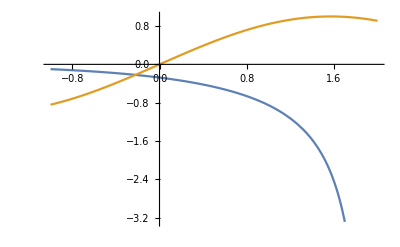

```mathematica
Plot[{Csch[x-2],Sin[x]},{x,-1,2}] (* Строим график с функциями по варианту, так будет легче увидеть корни*)
```

```mathematica
(* FindRoot[a,{x,b}] == а-выражение, b-стартовая позиция поиска ближайшего корня *)
FindRoot[{Csch[x-2] == Sin[x]},{x,0.3}]
```

{x→-0.221317}

## Задание 5

Найдите решение следующего дифференциального уравнения на заданном отрезке

```mathematica
sol=NDSolve[{y''[x]+2y'[x]*Tan[x]+ y[x]==0,y[0]==1,y'[0]==-2},y,{x,-3,2}] (*NDSolve - численное решение ДУ*)
```

{{y→InterpolatingFunction[…]}}

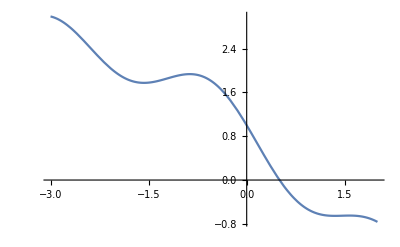

```mathematica
Plot[y[x]/.sol,{x,-3,2}] (* /. - заменить все *)
```

Найдите на заданном отрезке корни уравнения y(x)=0

```mathematica
sol1 = FindRoot[(y[x]/.sol[[1]])==0, {x,0.5}]
```

{x→0.502221}

Syntax::bktmop: Expression ":0412:044b:043f:043e:043b:043d:044f:0435:043c  :043f:043e:0438:0441:043a  :043a:043e:0440:043d:044f  :043f:0440:0438  :043f:043e:043c:043e:0449:0438  FindRoot, :0432  :043a:0430:0447:0435:0441:0442:0432:0435  :0432:044b:0440:0430:0436:0435:043d:0438:044f  :0431:0435:0440:0435:043c  :043f:0440:043e:0438:0437:0432:043e:0434:043d:0443:044e == 0)" has no opening "\"\<(\>\""\"\<\>\".

Найдите  значения производной y`(x) в точках, где y(x)=0

```mathematica
D[y[x]/.sol[[1]],x]/.sol1 (* D - дифференцировать (найти производную) при х=sol1 *)
```

-1.73327

ReplaceAll::reps: {sol4} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Выберите одну из точек, в которых производная функции y(x)  равна нулю, и вычислите значение функции в этой точке

```mathematica
sol3 = FindRoot[D[y[x]/.sol[[1]],x]==0,{x,1.3}] (* Выполняем поиск корня при помощи FindRoot, в качестве выражения берем производную == 0 *)
```

{x→1.35102}

```mathematica
y[x]/.sol[[1]]/.sol3
```

-0.654029

С помощью функции FindMinimum найдите точки, в которых функция y(x) имеет локальный минимум или максимум, и сравните полученные результаты со значениями, найденными в предыдущем пункте

```mathematica
FindMinimum[y[x]/.sol[[1]],{x,1.3}] (* Данная функция имеет похожую структуру с FindRoot, результат == результату в предыдущем пункте, т.к. в точке минимума(максимума) производная = 0 *)
```

{-0.654029,{x→1.35102}}

## Задание 6

Задайте произвольные численные значения параметров a, b, c, d, e в следующих зависимостях-Graphics-
Используя функцию Table, определите список численных данных, каждый элемент которого содержит два соответствующих элемента (x, y). Область изменения х и шаг выберите самостоятельно. С помощью функции Random внесите в каждой точке х случайное возмущение del y.

```mathematica
a=-1;b=3;c=4;d=5;e=8; (* Начальные значения а,б...e *)
(* Table[{x,y},{x,startPoint,endPoint,step}] в качестве y будет наше выражение, умноженное на погрешность (1 + случайное значение от -0.1 до 0.1) *)
dat1 = Table[{x, (a+b 0.5x+c x^2+d x^3+e x^4)(1+Random[Real,{-0.1,0.1}])},{x,-2,2,0.2}] 
dat2 = Table[{x, (a+b 0.5x+c Sin[x]+d Cos[x])(1+Random[Real,{-0.1,0.1}])},{x,-2,2,0.2}]
dat3 = Table[{x, (a+b 0.5x+c Sin[x]+d Cos[2 x])(1+Random[Real,{-0.1,0.1}])},{x,-2,2,0.2}]
dat4 = Table[{x, (a Sin[x]+b Cos[x]+c Sin[2 x]+d Cos[2 x])(1+Random[Real,{-0.1,0.1}])},{x,-2,2,0.2}]
```

{{-2.,100.559},{-1.8,61.8209},{-1.6,38.9731},{-1.4,19.5865},{-1.2,10.0949},{-1.,4.32135},{-0.8,1.14487},{-0.6,-0.52698},{-0.4,-1.15312},{-0.2,-1.27419},{0.,-0.981018},{0.2,-0.456695},{0.4,0.775138},{0.6,3.53799},{0.8,8.17412},{1.,15.8134},{1.2,34.5715},{1.4,55.7491},{1.6,85.219},{1.8,130.651},{2.,181.146}}

{{-2.,-8.76441},{-1.8,-8.54448},{-1.6,-7.31231},{-1.4,-6.61499},{-1.2,-4.89157},{-1.,-3.39803},{-0.8,-1.53647},{-0.6,-0.033261},{-0.4,1.41411},{-0.2,2.5549},{0.,4.08631},{0.2,5.34696},{0.4,5.67761},{0.6,6.47133},{0.8,6.44936},{1.,6.28462},{1.2,6.73111},{1.4,5.76658},{1.6,5.15022},{1.8,4.32294},{2.,3.26329}}

{{-2.,-11.678},{-1.8,-12.783},{-1.6,-13.573},{-1.4,-10.762},{-1.2,-10.136},{-1.,-7.85932},{-0.8,-4.83565},{-0.6,-2.29642},{-0.4,0.33186},{-0.2,2.31023},{0.,3.93701},{0.2,4.23795},{0.4,4.67735},{0.6,3.9648},{0.8,2.96375},{1.,1.81462},{1.2,0.906953},{1.4,0.302384},{1.6,0.389266},{1.8,1.17253},{2.,2.36757}}

{{-2.,-0.599786},{-1.8,-2.63322},{-1.6,-3.98923},{-1.4,-4.68583},{-1.2,-4.69997},{-1.,-3.55488},{-0.8,-1.36563},{-0.6,1.05267},{-0.4,3.71611},{-0.2,6.58715},{0.,7.54411},{0.2,9.06386},{0.4,8.43339},{0.6,7.30609},{0.8,4.91845},{1.,2.12591},{1.2,-0.88635},{1.4,-4.10336},{1.6,-6.46875},{1.8,-7.3709},{2.,-8.90437}}

Изобразите полученные точки на координатной плоскости

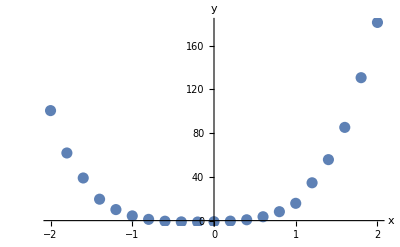

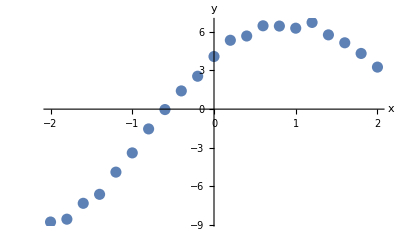

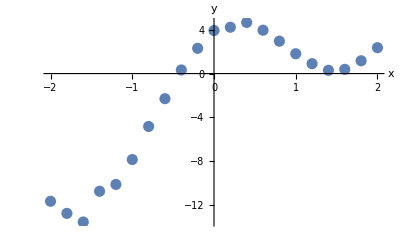

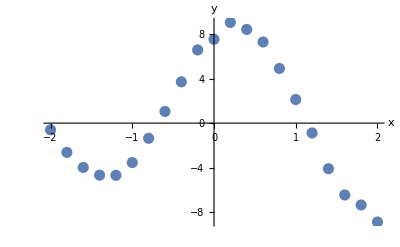

```mathematica
(* ListPlot - диаграмма разброса данных *)
p1 = ListPlot[dat1,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
p2 = ListPlot[dat2,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
p3 = ListPlot[dat3,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
p4 = ListPlot[dat4,PlotStyle->PointSize[0.02],AxesLabel->{"x","y"}]
```

С помощью функции Fit найдите наилучшую кривую, аппроксимирующую численные данные

```mathematica
(* Fit - функция для нахождения наилучших, с точки зрения метода наименьших квадратов, значения коэффициентов выражения
Fit[data, vars, x] - data-численные данные, vars-список функций, линейная комбинация которых должна аппроксимировать искомую зависимость. x-независимая переменная *)
y1 = Fit[dat1,{1, x, x^2,x^3,x^4}, x]
y2 = Fit[dat2,{1,x,Sin[x],Cos[x]}, x]
y3 = Fit[dat3,{1,x,Sin[x],Cos[2 x]}, x]
y4 = Fit[dat4,{Sin[x],Cos[x],Sin[2 x],Cos[2 x]}, x]
```

-1.36984+2.79891 x+5.02474 x^2+4.60546 x^3+7.66971 x^4

-0.949936+0.832723 x+4.90054 Cos[x]+4.93984 Sin[x]

-1.07201+2.15202 x+5.02268 Cos[2 x]+3.10878 Sin[x]

2.79998 Cos[x]+5.15499 Cos[2 x]-0.969459 Sin[x]+3.94404 Sin[2 x]

На одной координатной плоскости изобразите найденную кривую вместе с экспериментальными точками

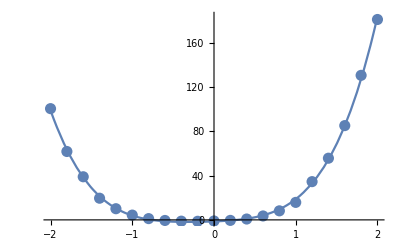

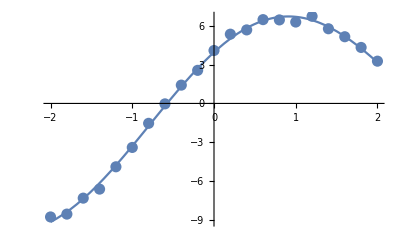

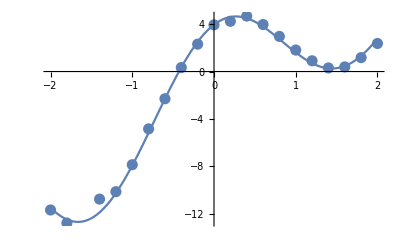

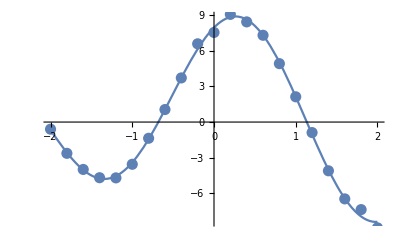

```mathematica
(* Plot - строим график функции *)
p11 := Plot[{y1},{x,-2,2}]
p21 := Plot[{y2},{x,-2,2}]
p31 := Plot[{y3},{x,-2,2}]
p41 := Plot[{y4},{x,-2,2}]
(* Показываем одновременно график функции, и диаграмму разброса данных при помощи Show *)
Show[p11,p1]
Show[p21,p2]
Show[p31,p3]
Show[p41,p4]
```